## 1. Frações contínuas e constante de Khinchin

### a)

```mathematica
khinchin1[epsilon_]:=
Module[{
khinchin=N[Khinchin,10],
k=2,
produtoParcial = 1.0,(* para k=1, Log[k,2]=0, logo produtoParcial[[1]]=termo[[1]]=1 *)
termo,
valorAprox,
n=1
},

While[True,
termo=N[(1+1/(k (k+2)))^(Log[2,k])];
produtoParcial*=termo;

If[Abs[produtoParcial-khinchin]<epsilon,
Return[{produtoParcial,k}],
(* else *)
k++
];

]
]
```

```mathematica
Table[khinchin1[10^(-n)],{n,1,4}]
```

{{2.58546,246},{2.67545,3547},{2.68445,45411},{2.68535,550885}}

### b)

```mathematica
$MaxExtraPrecision=100000000;
khinchin2[x_,epsilon_]:=
Module[{
khinchin=N[Khinchin,20],
n=2,
prod=1.0,
geom,
lista,
erro
},

lista=Rest[ContinuedFraction[x,1000000]];(* Ignoramos o termo a_0 *)
prod=lista[[1]];

While[n<=Length[lista],
prod*=lista[[n]];

geom=N[prod^(1.0/n)];

If[Abs[geom-khinchin]<epsilon,
Return[{geom,n}],
(* else *)
n++
];
];

(* Se o programa sair do ciclo While, não convergiu para o limite estabelecido. *)
Print["Aparentemente, não converge ou o limite não é a constante de Khinchin."];
Return[$Failed];
]
```

### c)

```mathematica
khinchin2[π,0.1]
khinchin2[π,0.01]
khinchin2[π,0.001]
khinchin2[π,0.0001]
```

{2.74351,16}

{2.69297,17}

{2.68533,117}

{2.68546,976}

```mathematica
khinchin2[ⅇ,0.01]
khinchin2[ⅇ,0.001]
```

{2.6945,76}

Aparentemente, não converge ou o limite não é a constante de Khinchin.

$Failed

```mathematica
khinchin2[Log[2],0.1]
khinchin2[Log[2],0.01]
khinchin2[Log[2],0.001]
khinchin2[Log[2],0.0001]
```

{2.60144,501}

{2.67695,3578}

{2.68458,4395}

{2.68545,4399}

```mathematica
khinchin2[(1+Sqrt[5])/2,0.0001]
```

Aparentemente, não converge ou o limite não é a constante de Khinchin.

$Failed

```mathematica
khinchin2[(Sqrt[3]+1)/2,0.0001]
```

Aparentemente, não converge ou o limite não é a constante de Khinchin.

$Failed

```mathematica
khinchin2[2^(1/3),0.1]
khinchin2[2^(1/3),0.01]
khinchin2[2^(1/3),0.001]
khinchin2[2^(1/3),0.0001]
```

{2.58708,29}

{2.69469,355}

{2.68498,357}

{2.68542,19306}

```mathematica
khinchin2[ⅇ^π,0.1]
khinchin2[ⅇ^π,0.01]
khinchin2[ⅇ^π,0.001]
khinchin2[ⅇ^π,0.0001]
```

{2.78313,188}

{2.68957,198}

{2.6855,1899}

{2.6855,1899}

```mathematica
khinchin2[Sin[1],0.1]
khinchin2[Sin[1],0.01]
khinchin2[Sin[1],0.001]
khinchin2[Sin[1],0.0001]
```

{2.78316,4}

{2.69408,57}

{2.68488,327}

{2.6855,1627}

```mathematica
khinchin2[Tan[1/2],0.1]
khinchin2[Tan[1/2],0.01]
```

{2.63596,9}

Aparentemente, não converge ou o limite não é a constante de Khinchin.

$Failed

### d)

Os valores necessários para esta alínea já foram calculados nas secções anteriores deste Notebook.

## 2. Raiz Digital

### b)

```mathematica
DigitalRoot[n_Integer]:=NestWhile[DigitSum,n,Function[x,IntegerLength[x]>1]]
```

### c)

#### a)

```mathematica
Map[DigitalRoot,Range[100]]
```

{1,2,3,4,5,6,7,8,9,1,2,3,4,5,6,7,8,9,1,2,3,4,5,6,7,8,9,1,2,3,4,5,6,7,8,9,1,2,3,4,5,6,7,8,9,1,2,3,4,5,6,7,8,9,1,2,3,4,5,6,7,8,9,1,2,3,4,5,6,7,8,9,1,2,3,4,5,6,7,8,9,1,2,3,4,5,6,7,8,9,1,2,3,4,5,6,7,8,9,1}

#### b)

```mathematica
First100Prime:=Map[Prime,Range[100]]
```

```mathematica
Map[DigitalRoot,First100Prime]
```

{2,3,5,7,2,4,8,1,5,2,4,1,5,7,2,8,5,7,4,8,1,7,2,8,7,2,4,8,1,5,1,5,2,4,5,7,4,1,5,2,8,1,2,4,8,1,4,7,2,4,8,5,7,8,5,2,8,1,7,2,4,5,1,5,7,2,7,4,5,7,2,8,7,4,1,5,2,1,5,4,5,7,8,1,7,2,8,7,2,4,8,2,1,5,4,8,5,8,1,1}

#### c)

```mathematica
First100Fibonacci:=Table[Fibonacci[n],{n,100}]
```

```mathematica
Map[DigitalRoot,First100Fibonacci]
```

{1,1,2,3,5,8,4,3,7,1,8,9,8,8,7,6,4,1,5,6,2,8,1,9,1,1,2,3,5,8,4,3,7,1,8,9,8,8,7,6,4,1,5,6,2,8,1,9,1,1,2,3,5,8,4,3,7,1,8,9,8,8,7,6,4,1,5,6,2,8,1,9,1,1,2,3,5,8,4,3,7,1,8,9,8,8,7,6,4,1,5,6,2,8,1,9,1,1,2,3}

#### d)

```mathematica
FermatFunction[n_Integer]:=2^2^n
```

```mathematica
First15Fermat:=Map[FermatFunction,Range[0,14]]
```

```mathematica
Map[DigitalRoot,First15Fermat]
```

{2,4,7,4,7,4,7,4,7,4,7,4,7,4,7}

#### e)

```mathematica
DenomFirst200ConvPi:=Denominator[Convergents[Pi,200]]
```

```mathematica
Map[DigitalRoot,DenomFirst200ConvPi]
```

{1,7,7,5,9,5,5,1,7,8,4,3,1,5,6,2,1,4,9,4,4,7,9,7,7,4,1,8,9,8,7,5,1,5,6,8,4,5,1,1,2,3,2,1,3,4,7,9,7,4,2,8,1,9,1,1,2,3,2,5,7,7,5,3,2,5,5,1,6,4,5,5,2,7,7,8,3,2,5,6,5,2,4,6,7,2,9,2,2,6,2,8,9,8,6,5,7,3,1,4,9,4,7,2,2,6,5,2,6,5,7,7,5,9,5,5,9,5,3,2,5,1,8,7,6,4,7,9,7,9,7,5,4,9,4,4,4,8,4,3,7,8,7,6,7,1,1,2,3,5,9,5,6,2,1,1,2,3,8,2,2,4,1,8,9,8,8,4,3,4,7,2,4,5,9,5,5,2,9,2,2,4,6,1,1,2,3,5,1,8,8,7,5,3,8,2,5,3,8,2}

#### f)

```mathematica
DenomFirst200ConvNeper:=Denominator[Convergents[E,200]]
```

```mathematica
Map[DigitalRoot,DenomFirst200ConvNeper]
```

{1,1,3,4,7,5,3,8,6,5,2,3,5,8,4,3,7,6,4,1,9,1,1,8,9,8,9,8,8,6,5,2,4,6,1,3,4,7,6,4,1,5,6,2,3,5,8,9,8,8,1,9,1,9,1,1,3,4,7,5,3,8,6,5,2,3,5,8,4,3,7,6,4,1,9,1,1,8,9,8,9,8,8,6,5,2,4,6,1,3,4,7,6,4,1,5,6,2,3,5,8,9,8,8,1,9,1,9,1,1,3,4,7,5,3,8,6,5,2,3,5,8,4,3,7,6,4,1,9,1,1,8,9,8,9,8,8,6,5,2,4,6,1,3,4,7,6,4,1,5,6,2,3,5,8,9,8,8,1,9,1,9,1,1,3,4,7,5,3,8,6,5,2,3,5,8,4,3,7,6,4,1,9,1,1,8,9,8,9,8,8,6,5,2,4,6,1,3,4,7}

### d)

#### 1)

#### a)

```mathematica
ListPlot[Map[DigitalRoot,Range[100]],Frame->True,FrameLabel->{"Ordem dos Números Inteiros Positivos","Raiz Digital"},PlotMarkers->"●"]
```

-Graphics-

#### b)

```mathematica
ListPlot[Map[DigitalRoot,First100Prime],Frame->True,FrameLabel->{"Ordem dos Números Primos","Raiz Digital"},PlotMarkers->"●"]
```

-Graphics-

#### c)

```mathematica
ListPlot[Map[DigitalRoot,First100Fibonacci],Frame->True,FrameLabel->{"Ordem dos Números de Fibonacci","Raiz Digital"},PlotMarkers->"●"]
```

-Graphics-

#### d)

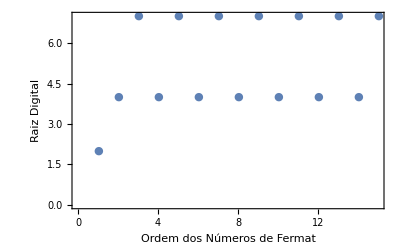

```mathematica
ListPlot[Map[DigitalRoot,First15Fermat],Frame->True,FrameLabel->{"Ordem dos Números de Fermat","Raiz Digital"},PlotMarkers->"●"]
```

#### e)

```mathematica
ListPlot[Map[DigitalRoot,DenomFirst200ConvPi],Frame->True,FrameLabel->{"Denominador da Ordem dos Convergentes da Função Contínua de Pi","Raiz Digital"},LabelStyle->{FontSize->9},PlotMarkers->"●"]
```

-Graphics-

#### f)

```mathematica
ListPlot[Map[DigitalRoot,DenomFirst200ConvNeper],Frame->True,FrameLabel->{"Denominador da Ordem dos Convergentes da Função Contínua de Neper","Raiz Digital"},LabelStyle->{FontSize->9},PlotMarkers->"●"]
```

-Graphics-

#### 2)

#### a)

```mathematica
ListOccPosInt:=Map[Function[x,Count[Map[DigitalRoot,Range[100]],x]],Range[9]]
```

```mathematica
DataPositiveInteger:=Transpose[{Range[9],ListOccPosInt}]
```

```mathematica
Grid[Prepend[DataPositiveInteger,{"Dígito","Número de Ocorrências"}],Frame->All]
```

Dígito | Número de Ocorrências
1 | 12
2 | 11
3 | 11
4 | 11
5 | 11
6 | 11
7 | 11
8 | 11
9 | 11

#### b)

```mathematica
ListOccPrime:=Map[Function[x,Count[Map[DigitalRoot,First100Prime],x]],Range[9]]
```

```mathematica
DataPrime:=Transpose[{Range[9],ListOccPrime}]
```

```mathematica
Grid[Prepend[DataPrime,{"Dígito","Número de Ocorrências"}],Frame->All]
```

Dígito | Número de Ocorrências
1 | 16
2 | 18
3 | 1
4 | 15
5 | 18
6 | 0
7 | 16
8 | 16
9 | 0

#### c)

```mathematica
ListOccFibonacci:=Map[Function[x,Count[Map[DigitalRoot,First100Fibonacci],x]],Range[9]]
```

```mathematica
DataFibonacci:=Transpose[{Range[9],ListOccFibonacci}]
```

```mathematica
Grid[Prepend[DataFibonacci,{"Dígito","Número de Ocorrências"}],Frame->All]
```

Dígito | Número de Ocorrências
1 | 22
2 | 9
3 | 9
4 | 8
5 | 8
6 | 8
7 | 8
8 | 20
9 | 8

#### d)

```mathematica
ListOccFermat:=Map[Function[x,Count[Map[DigitalRoot,First15Fermat],x]],Range[9]]
```

```mathematica
DataFermat:=Transpose[{Range[9],ListOccFermat}]
```

```mathematica
Grid[Prepend[DataFermat,{"Dígito","Número de Ocorrências"}],Frame->All]
```

Dígito | Número de Ocorrências
1 | 0
2 | 1
3 | 0
4 | 7
5 | 0
6 | 0
7 | 7
8 | 0
9 | 0

#### e)

```mathematica
ListDenomConvPi:=Map[Function[x,Count[Map[DigitalRoot,DenomFirst200ConvPi],x]],Range[9]]
```

```mathematica
DataDenomConvPi:=Transpose[{Range[9],ListDenomConvPi}]
```

```mathematica
Grid[Prepend[DataDenomConvPi,{"Dígito","Número de Ocorrências"}],Frame->All]
```

Dígito | Número de Ocorrências
1 | 23
2 | 30
3 | 15
4 | 23
5 | 32
6 | 13
7 | 27
8 | 19
9 | 18

#### f)

```mathematica
ListDenomConvNeper:=Map[Function[x,Count[Map[DigitalRoot,DenomFirst200ConvNeper],x]],Range[9]]
```

```mathematica
DataDenomConvNeper:=Transpose[{Range[9],ListDenomConvNeper}]
```

```mathematica
Grid[Prepend[DataDenomConvNeper,{"Dígito","Número de Ocorrências"}],Frame->All]
```

Dígito | Número de Ocorrências
1 | 33
2 | 11
3 | 23
4 | 23
5 | 22
6 | 22
7 | 12
8 | 33
9 | 21